# Cantor Dust

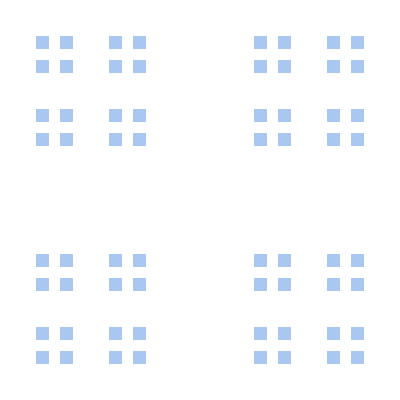

```mathematica
CantorDust[3,2]
```

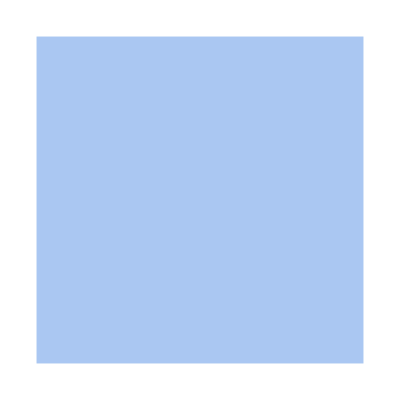
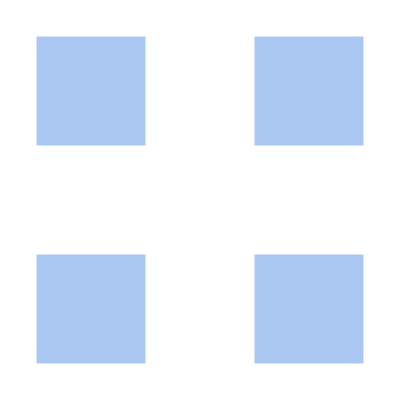
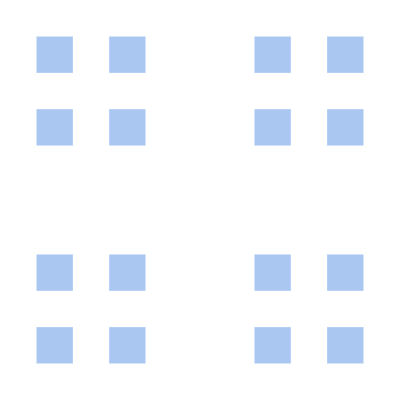
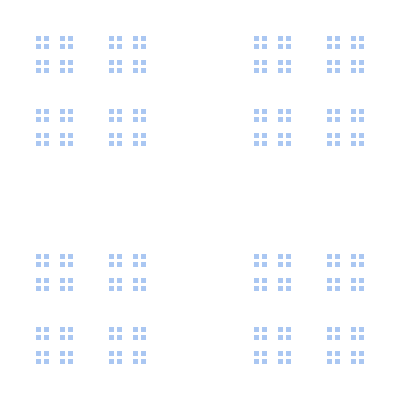
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[CantorDust[n,2],{n,0,4}]
```

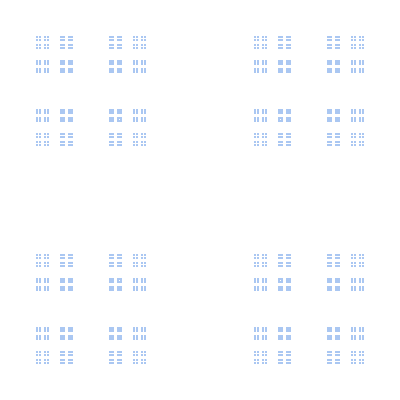
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- |

```mathematica
Multicolumn[Table[CantorDust[n,2],{n,0,6}],{3,Automatic}]
```

```mathematica
CantorDust[0,2,ImageSize->Full]
```

-Graphics-

```mathematica
FileNameJoin[{NotebookDirectory[],"cantor dust in two dimensions iteration ",ToString[6]," .svg"}]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\cantor dust in two dimensions iteration \6\ .svg

```mathematica
Table[Export[File[FileNameJoin[{NotebookDirectory[],"cantor dust in two dimensions iteration "<>ToString[n]<>".svg"}]],CantorDust[n,2,ImageSize->Full]],{n,0,6}]
```

{C:\Users\peter\Documents\GitHub\data-visualization-functions\cantor dust in two dimensions iteration 0.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\cantor dust in two dimensions iteration 1.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\cantor dust in two dimensions iteration 2.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\cantor dust in two dimensions iteration 3.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\cantor dust in two dimensions iteration 4.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\cantor dust in two dimensions iteration 5.svg,C:\Users\peter\Documents\GitHub\data-visualization-functions\cantor dust in two dimensions iteration 6.svg}

```mathematica
SystemOpen[Last[Table[Export[File[FileNameJoin[{NotebookDirectory[],"cantor dust in two dimensions iteration "<>ToString[n]<>".svg"}]],CantorDust[n,2]],{n,0,6}]]]
```